# O3: Snell’s Law and the Index of Refraction

Calvin Zikakis
Section 311
Drew Morrill
March 1 2017

## Introduction

The bending of light when traveling from one median to a different median is determined by Snell’s Law. In this lab, we investigated how light bends when traveling from air to plastic to air. In order to test Snell’s Law, we used a semicircular Lucite lens and a circular platform with an angle scale along its perimeter. A slit on the platform allowed a ray of light to enter the through the lens and create a projection on the angle scale. Next we took data at different measurements in order to get an average value of the index of refraction based off the angles of refraction. Snell’s Law allows us to be able to calculate this index with n = sinΘ / sinΘ. Part 2 of the lab consisted of measuring the values of n at the extreme red and violet ends of the visible spectrum. These measurements allowed us to estimate the wavelengths of red, yell, and violet light.

## Part 1: Index of Refraction of Lucite/Glass

1.48133

0.00424438

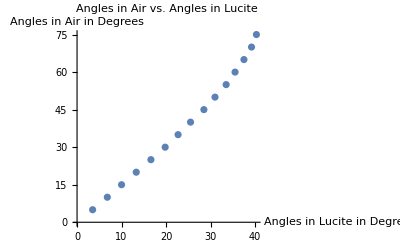

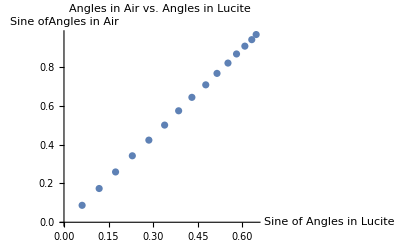

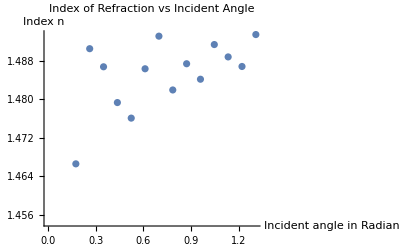

```mathematica
θadeg = {5, 10, 15, 20, 25, 30, 35, 40, 45, 50, 55, 60, 65, 70, 75};(*Air Angles in Degrees*)
θpdeg = {3.5, 6.8, 10, 13.3, 16.6, 19.8, 22.7, 25.5, 28.5, 31, 33.5, 35.5, 37.5, 39.2, 40.3};(*Plastic Angles in Degrees*)


θarad = θadeg*(π/180); (*Air Angles in Radians*)
θprad = θpdeg*(π/180);(*Plastic Angles in Radians*)
n  = Sin[θarad]/Sin[θprad];(*Index of Refraction*)

navg =( ∑_(i=1)^Length[n] n[[i]])/Length[n] (*Average n*)
nstv = √((∑_(i=1)^Length[n] (n[[i]]-navg)^2)/(Length[n]-1));
nsdom = nstv/√Length[n](*Uncertianty on n*)

θavsθp = Thread[{θpdeg,θadeg}];
SinθavsSinθp = Thread[{Sin[θprad],Sin[θarad]}];
nvsθa = Thread[{θarad,n}];

ListPlot[θavsθp,PlotLabel->"Angles in Air vs. Angles in Lucite",AxesLabel->{"Angles in Lucite in Degrees","Angles in Air in Degrees"}]
ListPlot[SinθavsSinθp,PlotLabel->"Angles in Air vs. Angles in Lucite",AxesLabel->{"Sine of Angles in Lucite","Sine ofAngles in Air"}]
ListPlot[nvsθa,PlotLabel->"Index of Refraction vs Incident Angle",AxesLabel->{"Incident angle in Radians","Index n"}]
```

Hence the measured index of refraction of Lucite is 1.481 ± 0.004. The graphs show a clear pattern in the data, graph one demonstrates how the angle of light in air varies from the angle in Lucite. Graph 2 shows the linear relationship between the sine of angles in the air vs the sine of angles in Lucite. Finally graph 3 demonstrates how the index of refraction measured varies at different angles. Graph 3 is supposed to be a straight line but has variation due to measurement error.

## Part 2: Dispersion of Lucite/Glass

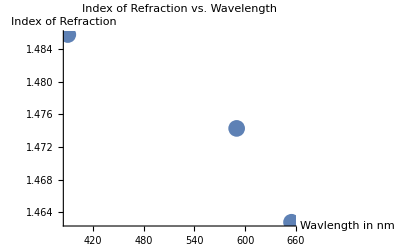

```mathematica
θp2deg = {42.0,40.0,35.0}; (*Incident Angle in Degrees*)
θReddeg = {72.5,73.0,57.8};(*Red Refracted Band in Degrees*)
θViodeg = {75.3,76.5,59.3};(*Violet Refracted Band in Degrees*)
θp2rad = θp2deg*(π/180);(*Incident Angle in Radians*)
θRedrad= θReddeg*(π/180);(*Red Refracted Band in Radians*)
θViorad= θViodeg*(π/180);(*Violet Refracted Band in Radians*)

nred = Sin[θRedrad]/Sin[θp2rad]; (*Index for Red light*)
nvio = Sin[θViorad]/Sin[θp2rad];(*Index for Violet Light*)

nravg = (∑_(i=1)^Length[nred] nred[[i]])/Length[nred];(*Average Index for Red Light*)
nvioavg = (∑_(i=1)^Length[nred] nvio[[i]])/Length[nvio];(*Average Index for Violet Light*)
nyellow = (nravg+nvioavg)/2;(*Average Index for Yellow Light*)

nvsλ = {{390,nvioavg},{590,nyellow},{655,nravg}}; (*n vs Wavlength (nm) Data*)
ListPlot[nvsλ,PlotLabel->"Index of Refraction vs. Wavelength",AxesLabel->{"Wavlength in nm","Index of Refraction"},PlotStyle->PointSize[0.03]]
```

My graph shows how index of refraction changes depending on wavelength. The indexes are very close in size, but I believe my data was measured well enough to provide evidence towards index of refraction being related to wavelength.

## Conclusion

In conclusion, this lab showed us an effective method for measuring an index of refraction. Using Snell’s law, light, and an angle scale, we were able to estimate the index of Lucite to 1.481 ± 0.004. Lucite has an index of 1.4896 ± 0.0001 giving our measurement a discrepancy of | 1.4896 - 1.481 | = 0.0086 which means the real value is 2.15 standard deviations away from our measurement value. The error in our estimated index value was 0.004 and the error of the accepted value is 0.0001. We can calculate the total error by √((0.0001)^2 + (0.004)^2) = 0.004.  Multiply this value by 3 in order to see if our measurements agree, 0.004 * 3  = 0.012. Because 0.012 > .0086, we can conclude that these values agree and attribute the slight difference in values to measurement error. This measurement error can come from a variety of things including the Lucite lens, it was hard to get perfectly center resulting in data that was not as accurate as it could be. Another factor that could have contributed to our error is reading the angle scale, the scale was not as precise as something such as a digital protractor would have been which contributed more to the measurement error. This lab showed the relationship between the index of refraction and the angle at which light is reflected, a higher index will make light refract at a much lower angle than it entered while a lower index makes light refract at a higher angle than the entry. 

	In part 2 of the lab, we measured that different wavelengths of light refract at different angles when going through a new median. This helps to explain how rainbows are formed by showing that when light reflects though a rain drop, the wavelengths can all reflect at different angles producing a prism effect when the light exits the drop. We also saw that different wavelengths of light refract at different indexes. Violet had the highest index of refraction in our testing at 1.485 while red had the lowest at 1.461, yellow then fell in the middle of the range with an index of refraction of 1.475. Different wavelengths refract differently because the speed of light in the median is a function of frequency (and index of refraction is just how quickly light is able to travel in a median when compared to air) which results in shorter wavelengths refracting more.